```mathematica
data=Import["E:\\Excel\\data.csv"];data=data⟦2;;⟧;amp=Interpolation[data⟦;;,{1,2}⟧];
phase=Interpolation[data⟦;;,{1,3}⟧];
```

```mathematica
fc=10*^3;sol=Solve[(amp[f]+20Log[10,Abs[(kp s+ki)/s]//.s->ⅈ 2π f//ComplexExpand]//.f->fc)==0∧ki/(2π kp)==fc/10,{kp,ki},Reals]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{kp→-0.0168729,ki→-106.016},{kp→0.0168729,ki→106.016}}

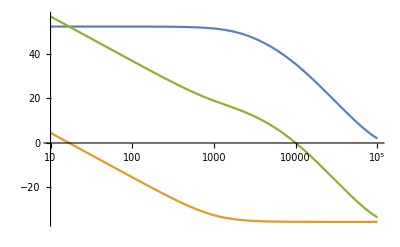

```mathematica
LogLinearPlot[{amp[f],20Log[10,Abs[(kp s+ki)/s]//.{s->ⅈ 2π f}//.sol⟦2⟧],amp[f]+20Log[10,Abs[(kp s+ki)/s]//.s->ⅈ 2π f//.sol⟦2⟧]}//Evaluate,{f,10,100*^3},PlotRange->All]
```

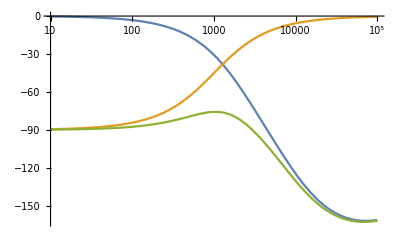

```mathematica
LogLinearPlot[{phase[f],180/π Arg[(kp s+ki)/s]//.{s->ⅈ 2π f}//.sol⟦2⟧,phase[f]+180/π Arg[(kp s+ki)/s]//.{s->ⅈ 2π f}//.sol⟦2⟧},{f,10,100*^3},PlotRange->All]
```